```mathematica
(*
AError=(Total[(GenData-Data)^2]/(DataLength-varamt))^0.5;
*)
```

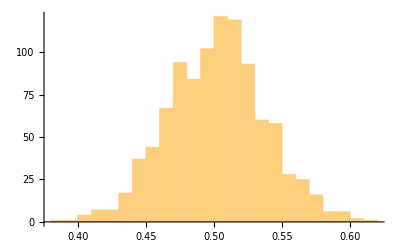
{-Graphics-,0.501843,0.0356243}

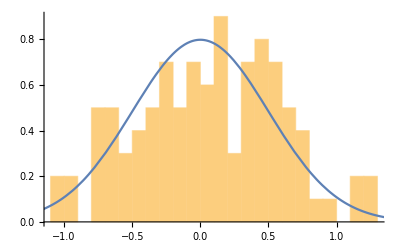
{-Graphics-,0.529255,0.532358}

```mathematica
Dev=0.5;
DataLength=100;
VarAmt=1;
f=Exp@(-0.2#)+#&;
CheckVariance[]:=(
PureData=f/@Range@DataLength;
NoisyData=((RandomVariate@NormalDistribution[0,Dev]+f@#)&/@Range@DataLength);
(*ListPlot[{NoisyData,PureData}]*)
Return[(Total[(NoisyData-PureData)^2]/(DataLength-VarAmt))^0.5];
);
	
{
Histogram@#,
Mean@#,
StandardDeviation@#
}&@Table[CheckVariance[],{i,1000}]

{
Show@@{Histogram[#,30,"PDF"],Plot[(PDF@NormalDistribution[0,Dev])@t,{t,-4Dev,4Dev}]},
StandardDeviation@#,
(Total[#^2]/(DataLength-VarAmt))^0.5
}&@(NoisyData-PureData)
```